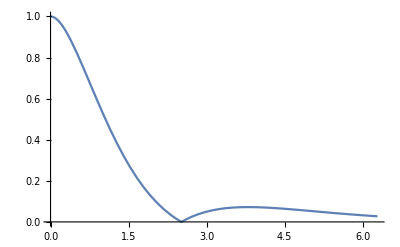

```mathematica
Plot[Abs[1+Δx-5/9(Δx)^2]Exp[-Δx],{Δx,0,2π},PlotRange->Full]
```

The intensity at the exit of a defocused three-blade NI is I=∫2|trr|^2(1+cos(ϕ+2πδy/Δ))dy where the integral is taken over the angular deviation parameter y=δθ/σ;

```mathematica
IH[x_]:=Integrate[16/(45π)(40 y^2+1)/((1+y^2)^4)(1+Cos[ 2π x y]),{y,-∞,∞}]  (*x=Δz/Subscript[Δ, H], that is the defocusing over the Pendellosung period*)
```

$Aborted

```mathematica
Integrate[16/(45π)(40 y^2+1)/((1+y^2)^4),{y,-∞,∞}]
```

1

The contrast function can be expressed as: with the average taken over uniformly distributed y

```mathematica
FH41[x_]:=NIntegrate[16/(45π)(40 y^2+1)/((1+y^2)^4)Exp[I π x y],{y,-200,200}]
```

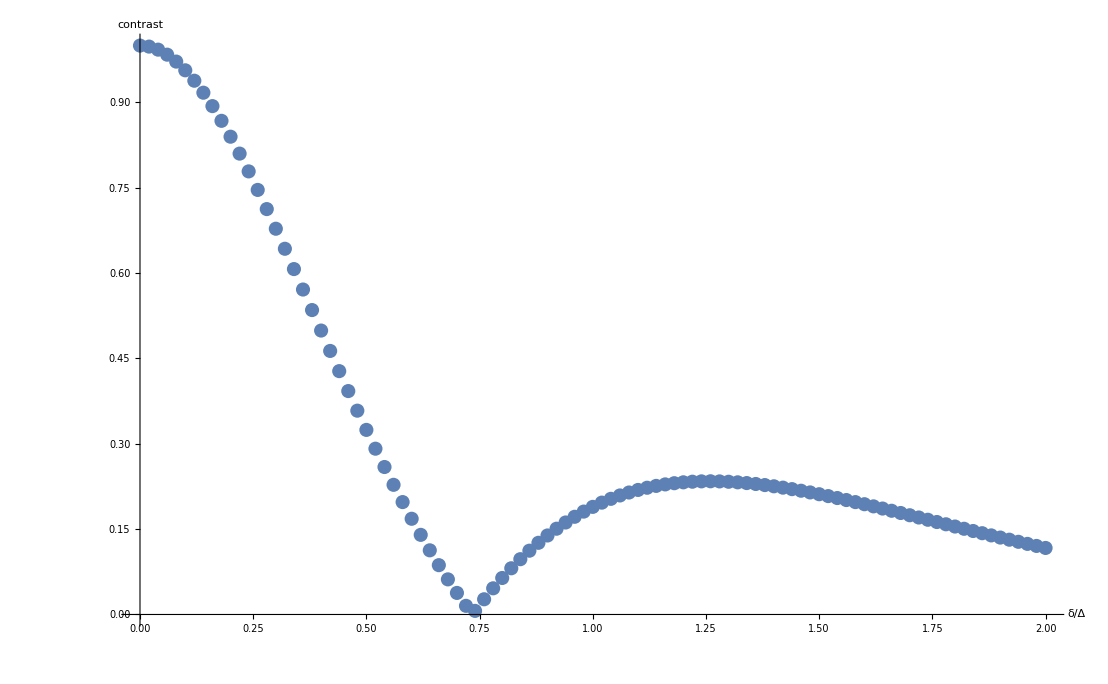

```mathematica
ListPlot[Table[{x,Abs[FH41[x]]},{x,0,2,.02}],PlotRange->All, AxesLabel->{"δ/Δ","contrast"},AxesStyle->Directive[Black,20]]
```

For 0.44 nm and Si [111] neutrons, Δ_H= 34.4 μm, and for 2.2 it is 90.4 μm. So for a contrast of 0.37, we have about δ/Δ=0.2

```mathematica
a=5.431*10^-10;
Tan[ArcSin[1.1*√3/(5.431)]]*90.4
```

33.8656

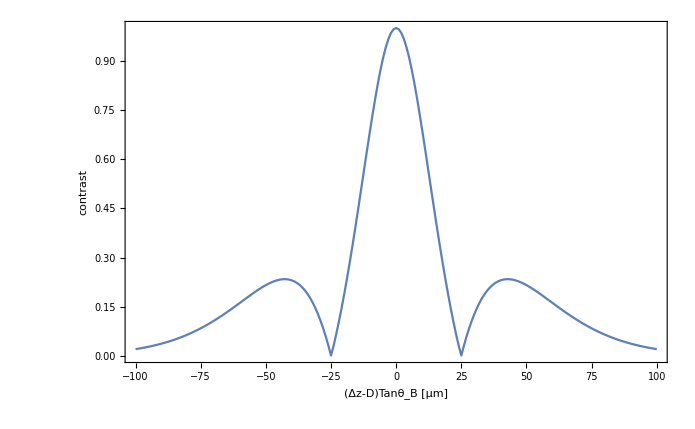

```mathematica
ListLinePlot[Table[{x,Abs[FH41[x/34]]},{x,-100,100,1}],PlotRange->All, Frame->True,FrameLabel->{"(Δz-D)Tanθ_B [μm]","contrast"},FrameStyle->Directive[Black,20]]
```

```mathematica
ListPlot[Table[{x,Abs[FH41[x/34]]},{x,-100,100,1}],PlotRange->All,PlotStyle->Black, Frame->True,FrameLabel->{"(Δz-D)Tanθ_B [μm]","contrast"},FrameStyle->Directive[Black,20]]
```

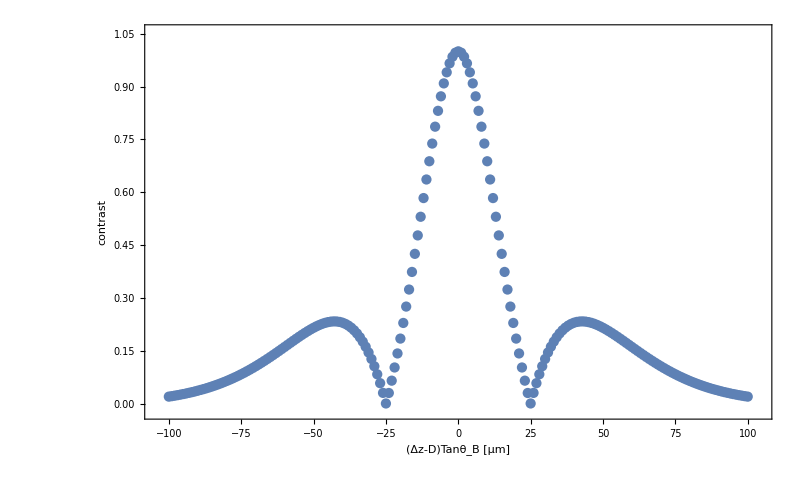

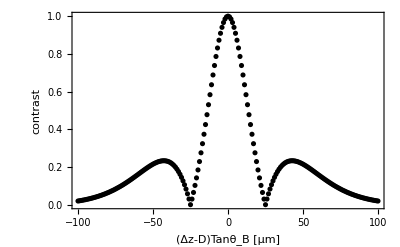

```mathematica
ListPlot[Table[{x,Abs[FH41[x/34]]},{x,-100,100,1}],PlotRange->All,PlotStyle->Black, Frame->True,FrameLabel->{"(Δz-D)Tanθ_B [μm]","contrast"},FrameStyle->Directive[Black,20]]
```

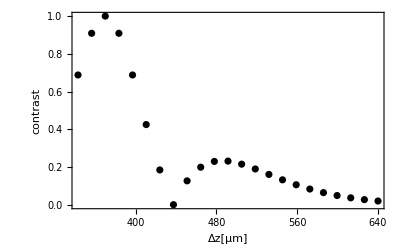

```mathematica
ListPlot[Table[{x/.37+370,Abs[FH41[x/34]]},{x,-10,100,5}],PlotRange->All,PlotStyle->Black, Frame->True,FrameLabel->{"Δz[μm]","contrast"},FrameStyle->Directive[Black,20]]
```

```mathematica
FH42[x_]:=NIntegrate[16/(45π)(40 y^2+1)/((1+y^2)^4)Exp[I π  y],{y,-200,200}];
```

```mathematica
ListPlot[Table[{x,Abs[FH41[x/0.37 +]]},{x,-1000,1000,1}],PlotRange->All, Frame->True,FrameLabel->{"(Δz-D)Tanθ_B [μm]","contrast"},FrameStyle->Directive[Black,20]]
```

1+ⅈ π y x-1/2 (π^2 y^2) x^2-1/6 ⅈ π^3 y^3 x^3+O[x]^4

```mathematica
FH42[x_]=Integrate[16/(45π)(40 y^2+1)/((1+y^2)^4)(1+ⅈ π y x-1/2 (π^2 y^2) x^2),{y,-∞,∞}]
```

1-(41 π^2 x^2)/90

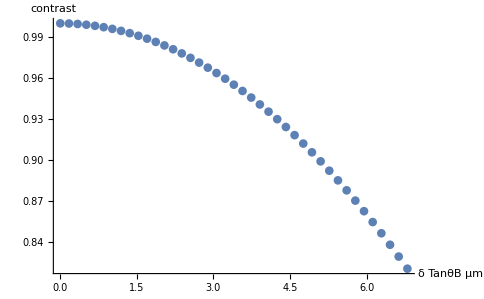

```mathematica
ListPlot[Table[{x*34,Abs[FH42[x]]},{x,0,.2,.005}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

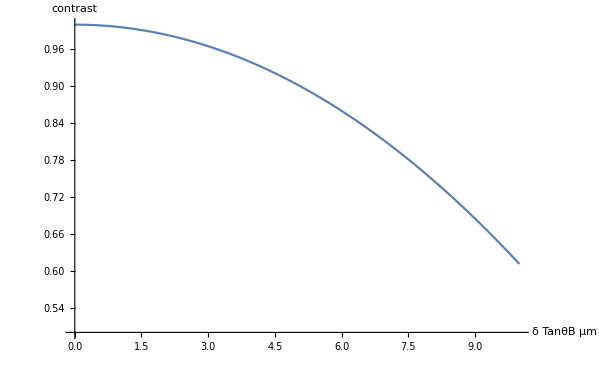

```mathematica
Plot[Abs[FH42[x/34]],{x,0,10},PlotRange->{.5,1}, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

```mathematica
FH43[x_,a1_]:=9.73NIntegrate[((Sin[a1 √(1+y^2)]^2)/(1+y^2))^3(1-(Sin[a1 √(1+y^2)]^2)/(1+y^2))(Exp[I π x y]),{y,-200,200}]
```

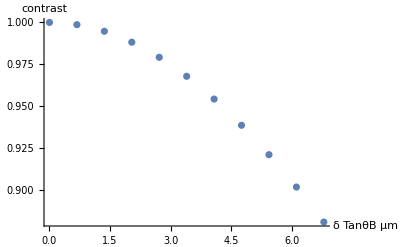

```mathematica
ListPlot[Table[{x*34,Abs[FH43[x,74]]},{x,0,.2,.02}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

```mathematica
FH43[0,74]
```

0.999988

```mathematica
1/0.10277370626062873
```

9.73012

```mathematica
Integrate[Sin[x]^8,{x,0,2Pi}]
```

(35 π)/64

```mathematica
FH44[x_,a1_]:=128/(15Pi)NIntegrate[((Sin[a1 √(1+y^2)]^2)/(1+y^2))^3(1-(Sin[a1 √(1+y^2)]^2)/(1+y^2))(Exp[I π x y]),{y,-200,200}]
```

```mathematica
Ano1=FH44[0,74]
```

0.279159

```mathematica
ListPlot[Table[{x,Abs[FH44[x/34,74]]/Ano1},{x,0,.2,.02}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

-Graphics-

```mathematica
ListPlot[Table[{x,Abs[FH44[x,74]]/Ano1},{x,-100,100,1}],PlotRange->All, AxesLabel->{"δ TanθB μm","contrast"},AxesStyle->Directive[Black,20]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.}. NIntegrate obtained -0.000149526 + 3.79204×10^-6\ ⅈ and 0.000181399 for the integral and error estimates.

$Aborted

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.}. NIntegrate obtained -0.000149526 + 3.79204×10^-6\ ⅈ and 0.000181399 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.78125}. NIntegrate obtained 0.0000431962  - 0.000165908\ ⅈ and 0.0000732191 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.}. NIntegrate obtained 0.000139698  - 0.0000944459\ ⅈ and 0.0000335287 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

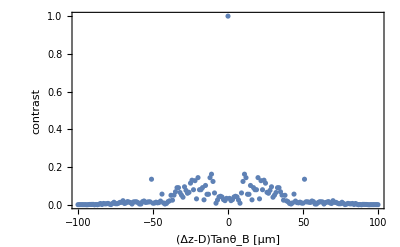

```mathematica
ListPlot[Table[{x,Abs[FH44[x,74]]/Ano1},{x,-100,100,1}],PlotRange->All, Frame->True,FrameLabel->{"(Δz-D)Tanθ_B [μm]","contrast"},FrameStyle->Directive[Black,20]]
```

```mathematica
Pi/0.0850
```

36.9599

```mathematica
ListPlot[Table[{x,Abs[FH41[x/34]]},{x,-100,100,1}],PlotRange->All,PlotStyle->Black, Frame->True,FrameLabel->{"(Δz-D)Tanθ_B [μm]","contrast"},FrameStyle->Directive[Black,20]]
```